# Enhancing the SpokenString function output based on the input symbolic structure

Renan Germano

Mackenzie Presbyterian University

When dealing with graphs and images, the current SpokenString function returns a not significant text to the describe the input. The objective of the present project is to enhance this output by developing an algorithm that is capable of  better describing the input, based on its symbolic structure. Thinking about accessibility for visually impaired, this text could be used as an automatic generated alternative description for images and related contents.

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

### Already build-in functions to describe Wolfram Language expressions

```mathematica
redSphere=Graphics3D[{Red,Sphere[]}]
```

-Graphics3D-

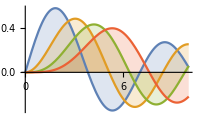

```mathematica
complexGraph=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

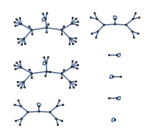

```mathematica
someGraphs=GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

```mathematica
RelationshipGraphs[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,{EntityProperty["WolframLanguageSymbol","RelationshipGraph"],EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]}]
```

#### SpokenString

```mathematica
?SpokenString
SpokenString@redSphere
SpokenString@complexGraph
SpokenString@someGraphs
```

a three-dimensional graphic consisting of a sphere

a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points

a graphic consisting of 103 arrows and 103 disks

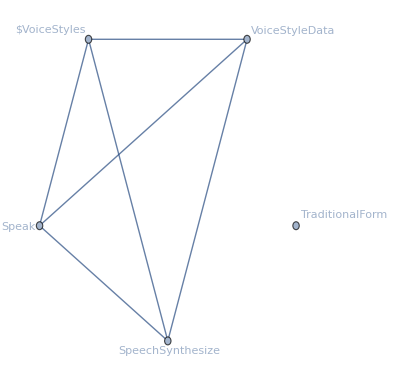
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@SpokenString
```

#### TextString

```mathematica
?TextString
TextString@redSphere
TextString@complexGraph
TextString@someGraphs
```

Graphics3D[{RGBColor[1, 0, 0], Sphere[{0, 0, 0}]}]

Graphics[…]

Graphics[…]

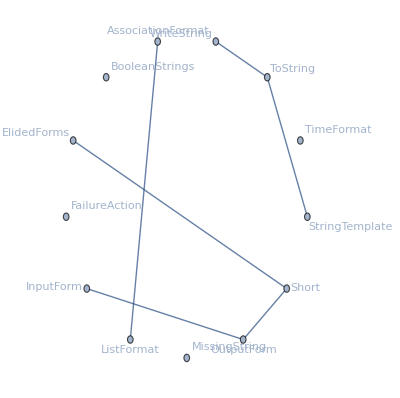
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@TextString
```

#### ToString

```mathematica
?ToString
ToString@redSphere
ToString@complexGraph
ToString@someGraphs
```

-Graphics3D-

-Graphics-

-Graphics-

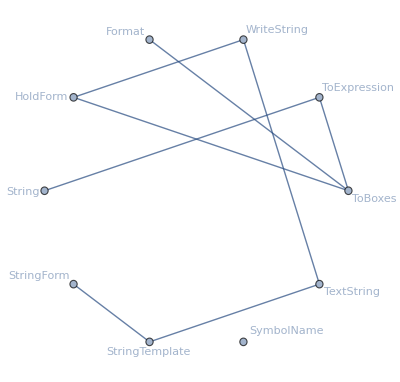
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@ToString
```

### Describing Colors

#### Named Colors

```mathematica
?WolframLanguageData
```

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```

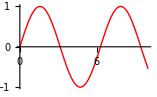
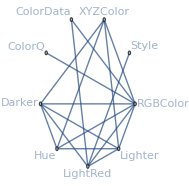
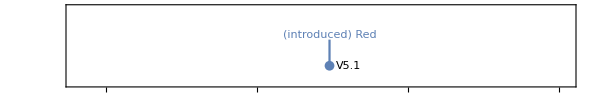
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
functionalityAreaOfAllWLSymbols={#, EntityValue[#,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}&/@wlSymbols;
```

```mathematica
colorSymbols=Select[functionalityAreaOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

Black | RGBColor[0., 0., 0.] | Black | {Simplified Chinese→黑色,Traditional Chinese→黑,French→noir,German→schwarz,Modern Greek→μαύρο,Japanese→黒,Korean→검정,Lithuanian→juodas,Polish→czarny,Portuguese→preto,Russian→чёрный,Spanish→negro,Ukrainian→чорний,Vietnamese→đen}
Blue | RGBColor[0., 0., 1.] | Blue | {Simplified Chinese→蓝色,Traditional Chinese→藍色,French→bleu,German→blau,Modern Greek→μπλε,Japanese→青,Korean→파랑,Lithuanian→mėlynas,Polish→niebieski,Portuguese→azul,Russian→синий,Spanish→azul,Ukrainian→синій,Vietnamese→xanh da trời}
Brown | RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412] | Brown | {Simplified Chinese→棕色,Traditional Chinese→棕色,French→marron,German→braun,Modern Greek→καφέ,Japanese→茶色,Korean→갈색,Lithuanian→rudas,Polish→brązowy,Portuguese→marrom,Russian→коричневый,Spanish→marrón,Ukrainian→коричневий,Vietnamese→nâu}
Cyan | RGBColor[0., 1., 1.] | Cyan | {Simplified Chinese→蓝绿色,Traditional Chinese→藍綠色,French→cyan,German→blaugrün,Modern Greek→κυανό,Japanese→シアン色,Korean→청록색,Lithuanian→žalsvai mėlynas,Polish→cyjan,Portuguese→azul turquesa,Russian→голубой,Spanish→cian,Ukrainian→блакитний,Vietnamese→lục lam}
Gray | RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Gray | {Simplified Chinese→灰色,Traditional Chinese→灰,French→gris,German→grau,Modern Greek→γκρι,Japanese→灰色,Korean→회색,Lithuanian→pilkas,Polish→szary,Portuguese→cinza,Russian→серый,Spanish→gris,Ukrainian→сірий,Vietnamese→xám}
Green | RGBColor[0., 0.5019607843137255, 0.] | Green | {Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
LightBlue | RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726] | LightBlue | {Simplified Chinese→浅蓝色,Traditional Chinese→淡藍色,French→bleu clair,German→hellblau,Modern Greek→γαλάζιο,Japanese→水色,Korean→하늘색,Lithuanian→šviesiai mėlyna,Polish→jasnoniebieski,Portuguese→azul claro,Russian→светло-синий,Spanish→azul claro,Ukrainian→світло-синій,Vietnamese→xanh da trời nhạt}
LightCyan | RGBColor[0.87843137254902, 1., 1.] | LightCyan | {Simplified Chinese→淡青色,Traditional Chinese→淡青色,French→cyan clair,German→helles Blaugrün,Modern Greek→ανοιχτό κυανό,Japanese→薄いシアン色,Korean→밝은 청록색,Lithuanian→šviesiai žalsvai mėlyna,Polish→jasny cyjan,Portuguese→azul turquesa claro,Russian→светло-голубой,Spanish→cian claro,Ukrainian→світло-блакитний,Vietnamese→lục lam nhạt}
LightGreen | RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411] | LightGreen | {Simplified Chinese→浅绿,Traditional Chinese→淡綠色,French→vert clair,German→hellgrün,Modern Greek→ανοιχτό πράσινο,Japanese→薄緑色,Korean→연두색,Lithuanian→šviesiai žalia,Polish→jasnozielony,Portuguese→verde claro,Russian→светло-зелёный,Spanish→verde claro,Ukrainian→світло-зелений,Vietnamese→xanh lá cây nhạt}
LightPink | RGBColor[1., 0.7137254901960784, 0.7568627450980392] | LightPink | {Simplified Chinese→浅粉色,Traditional Chinese→淡粉色,French→rose clair,German→hellrosa,Modern Greek→ανοιχτό ροζ,Japanese→薄いピンク色,Korean→연분홍색,Lithuanian→šviesiai rausvos,Polish→jasnoróżowy,Portuguese→rosa claro,Russian→светло-розовый,Spanish→rosa claro,Ukrainian→світло-рожевий,Vietnamese→hồng nhạt}
LightYellow | RGBColor[1., 1., 0.87843137254902] | LightYellow | {Simplified Chinese→浅黄色,Traditional Chinese→淡黃色,French→jaune clair,German→hellgelb,Modern Greek→ανοιχτό κίτρινο,Japanese→薄い黄色,Korean→담황색,Lithuanian→šviesiai geltonos,Polish→jasnożółty,Portuguese→amarelo claro,Russian→светло-жёлтый,Spanish→amarillo claro,Ukrainian→світло-жовтий,Vietnamese→vàng nhạt}
Magenta | RGBColor[1., 0., 1.] | Magenta | {Simplified Chinese→品红色,Traditional Chinese→品紅色,French→magenta,German→magenta,Modern Greek→ματζέντα,Japanese→マジェンタ色,Korean→마젠타 색,Lithuanian→tamsiai raudonas,Polish→magenta,Portuguese→magenta,Russian→малиновый,Spanish→magenta,Ukrainian→малиновий,Vietnamese→đỏ tươi}
Orange | RGBColor[1., 0.6470588235294118, 0.] | Orange | {Simplified Chinese→橙色,Traditional Chinese→橙色,French→orange,German→orange,Modern Greek→πορτοκαλί,Japanese→オレンジ色,Korean→오렌지,Lithuanian→oranžinis,Polish→pomarańczowy,Portuguese→laranja,Russian→оранжевый,Spanish→naranja,Ukrainian→помаранчевий,Vietnamese→cam}
Pink | RGBColor[1., 0.7529411764705882, 0.796078431372549] | Pink | {Simplified Chinese→粉色,Traditional Chinese→粉紅色,French→rose,German→rosa,Modern Greek→ροζ,Japanese→ピンク色,Korean→분홍색,Lithuanian→rožinis,Polish→różowy,Portuguese→rosa,Russian→розовый,Spanish→rosa,Ukrainian→рожевий,Vietnamese→hồng}
Purple | RGBColor[0.5019607843137255, 0., 0.5019607843137255] | Purple | {Simplified Chinese→紫色,Traditional Chinese→紫色,French→violet,German→lila,Modern Greek→μωβ,Japanese→紫色,Korean→보라색,Lithuanian→purpurinis,Polish→purpurowy,Portuguese→roxo,Russian→фиолетовый,Spanish→púrpura,Ukrainian→фіолетовий,Vietnamese→tím}
Red | RGBColor[1., 0., 0.] | Red | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
White | RGBColor[1., 1., 1.] | White | {Simplified Chinese→白色,Traditional Chinese→白色,French→blanc,German→weiß,Modern Greek→λευκό,Japanese→白,Korean→흰색,Lithuanian→baltas,Polish→biały,Portuguese→branco,Russian→белый,Spanish→blanco,Ukrainian→білий,Vietnamese→trắng}
Yellow | RGBColor[1., 1., 0.] | Yellow | {Simplified Chinese→黄色,Traditional Chinese→黄色,French→jaune,German→gelb,Modern Greek→κίτρινο,Japanese→黄色,Korean→노란색,Lithuanian→geltonas,Polish→żółty,Portuguese→amarelo,Russian→жёлтый,Spanish→amarillo,Ukrainian→жовтий,Vietnamese→vàng}

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

```mathematica
MyColorDistance[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
MyColorDistance[Red,Red]
MyColorDistance[Red,Green]
MyColorDistance[Red,Blue]
MyColorDistance[Red,Pink]
MyColorDistance[Red,Black]
```

0.

0.666667

0.666667

0.333333

MyColorDistance[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.32791526849313435, 0.4964549822940518, 0.007826250271401713]

RGBColor[0., 0.5019607843137255, 0.]

Green

verde

```mathematica
Clear[Description]
```

```mathematica
Description[color_RGBColor]:=Description[color]=namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]@"Name"
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.45366306606643003, 0.9516244941610723, 0.14475745825416864]

LightGreen

```mathematica
tests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests,{5,20,2}]
```

{RGBColor[{0.6339147912991396, 0.8836724490828214, 0.5025300318667754}] | LightGreen
RGBColor[{0.7331321247007971, 0.8481941882376165, 0.8994643061649101}] | LightBlue
RGBColor[{0.39716671146615945, 0.20646517593457214, 0.8440690509072761}] | Blue
RGBColor[{0.22101296788590719, 0.85871062958608, 0.7288167774804846}] | Cyan
RGBColor[{0.45870575014909054, 0.7507580517748269, 0.6479338027402342}] | LightBlue
RGBColor[{0.95943785466552, 0.8036910338178636, 0.15710283303551997}] | Orange
RGBColor[{0.24100460247494038, 0.4996181283185388, 0.8106013065591815}] | Gray
RGBColor[{0.1320101867156367, 0.3625438792923217, 0.2584402018635983}] | Gray
RGBColor[{0.7482697889007397, 0.8981414691746366, 0.26518709296701615}] | Yellow
RGBColor[{0.727762013093137, 0.6425214344974957, 0.6222223762284855}] | Gray
RGBColor[{0.9988470021896747, 0.9458626516506294, 0.27794443782222533}] | Yellow
RGBColor[{0.7200789875403606, 0.02474620842495434, 0.7806984708507987}] | Magenta
RGBColor[{0.5172791883275973, 0.8444995172654215, 0.36288312778119636}] | LightGreen
RGBColor[{0.9815481011307972, 0.5991177766795974, 0.6860035397096189}] | LightPink
RGBColor[{0.1984243088481461, 0.045871100615166194, 0.8186136738539027}] | Blue
RGBColor[{0.8512152977922398, 0.7441431577791837, 0.38625741951446946}] | Orange
RGBColor[{0.8856100182329596, 0.7124526314433663, 0.054101541956420585}] | Orange
RGBColor[{0.7513184981611991, 0.3356835593396823, 0.5762463205892268}] | Purple
RGBColor[{0.46115544390613494, 0.13781919901132245, 0.7726502549457359}] | Purple
RGBColor[{0.16361200899956696, 0.1573624817089967, 0.5257852342081006}] | Purple,RGBColor[{0.47176473421750265, 0.9772178161169442, 0.005529728995894434}] | Yellow
RGBColor[{0.8139534483143693, 0.26304966087878645, 0.8938469582510347}] | Magenta
RGBColor[{0.9159923125100118, 0.12174212380885807, 0.8290696334336429}] | Magenta
RGBColor[{0.8489960449883462, 0.47928203254023916, 0.3360296876629436}] | Brown
RGBColor[{0.7646610409958932, 0.9807813081898555, 0.14127146479676989}] | Yellow
RGBColor[{0.8037392487441262, 0.5724363475283116, 0.9054894895895145}] | Pink
RGBColor[{0.9270484072892555, 0.4808280331607391, 0.9587775288726137}] | Purple
RGBColor[{0.6692896178545866, 0.775140980965797, 0.4488613758429454}] | LightGreen
RGBColor[{0.4897480686949187, 0.1328042302044683, 0.9969012790429943}] | Blue
RGBColor[{0.04955358616279426, 0.8930182881919713, 0.20264275729790748}] | LightGreen
RGBColor[{0.6138086741349824, 0.28303126108747634, 0.6267722995255418}] | Purple
RGBColor[{0.9529774441395928, 0.960297318599854, 0.1129969408960485}] | Yellow
RGBColor[{0.33141753123512196, 0.08807051879293937, 0.28004640864760666}] | Purple
RGBColor[{0.14401826896173175, 0.6577912050228036, 0.19831465573077067}] | Green
RGBColor[{0.24195639090303178, 0.13334219597778008, 0.6001788500188843}] | Purple
RGBColor[{0.47724227400135977, 0.8599122933255587, 0.7530795623202486}] | Cyan
RGBColor[{0.1606429110185612, 0.6341306642073081, 0.3467357281842707}] | Green
RGBColor[{0.5867687602620946, 0.39787205048086016, 0.9192559138839986}] | Purple
RGBColor[{0.9802272242303176, 0.5517633964932838, 0.9038485599697454}] | LightPink
RGBColor[{0.8569063814711468, 0.8498145643642132, 0.7993494157473531}] | White,RGBColor[{0.1239659281232286, 0.6920427114326677, 0.3711032303095825}] | Green
RGBColor[{0.4691695810312104, 0.5280846768163006, 0.8611085319366425}] | Gray
RGBColor[{0.6965724813181402, 0.36524399397664253, 0.5464432639077883}] | LightPink
RGBColor[{0.14017752355666424, 0.4030077098009268, 0.3547167754911391}] | Gray
RGBColor[{0.4929254758379322, 0.20443846026512924, 0.9579130917665335}] | Blue
RGBColor[{0.4960015451419726, 0.8712140336764538, 0.8616189202871267}] | LightBlue
RGBColor[{0.6791672971580511, 0.8566023196101769, 0.026449544494625776}] | Yellow
RGBColor[{0.07975191544519644, 0.5019911396401187, 0.29353107912957044}] | Green
RGBColor[{0.9300456994721087, 0.6819889475226564, 0.2783496819225546}] | Orange
RGBColor[{0.6827707832372503, 0.08915425749017891, 0.8230509860631212}] | Magenta
RGBColor[{0.8821089213373314, 0.39290202596143686, 0.3517251116046245}] | Brown
RGBColor[{0.09052241755274659, 0.33608688814169096, 0.23100764548314245}] | Gray
RGBColor[{0.9505860782986582, 0.9555557828815362, 0.31832695256258225}] | Yellow
RGBColor[{0.8839752742684928, 0.4039636548336216, 0.7659817607612736}] | Purple
RGBColor[{0.4552192869242868, 0.05734790726142869, 0.20579695609346138}] | Brown
RGBColor[{0.23201419848674787, 0.11254850932006621, 0.006858528878208148}] | Black
RGBColor[{0.244945928011578, 0.5835129837917454, 0.8044712497518836}] | LightBlue
RGBColor[{0.9524467023428322, 0.6873035852078571, 0.8539323195252768}] | Pink
RGBColor[{0.6112748166299704, 0.10420038068913895, 0.11599231042663938}] | Brown
RGBColor[{0.08532716472776225, 0.073067617966738, 0.024163417544232457}] | Black,RGBColor[{0.972101528057919, 0.29732963518622735, 0.5747442235140523}] | Brown
RGBColor[{0.21689287621759767, 0.4351566897765762, 0.5456752416627779}] | Gray
RGBColor[{0.8141639105687406, 0.7644470816174134, 0.27750694734173864}] | Orange
RGBColor[{0.5557862246357226, 0.7754717585623363, 0.005389307971565671}] | Yellow
RGBColor[{0.5355089349036193, 0.45677274793384237, 0.31348789455426385}] | Gray
RGBColor[{0.8163806814685632, 0.42467765214847675, 0.7486233537317251}] | Purple
RGBColor[{0.6070918205614526, 0.4756858961096433, 0.04086898097754843}] | Orange
RGBColor[{0.4603534854424318, 0.07560546881874597, 0.7663039804764009}] | Purple
RGBColor[{0.8850054527030946, 0.9039880546968317, 0.06618444425244063}] | Yellow
RGBColor[{0.3220734222046504, 0.2663311448682568, 0.09839963197708346}] | Gray
RGBColor[{0.10659189256439539, 0.021025271325809225, 0.08650891080886924}] | Black
RGBColor[{0.32576810835332237, 0.4926139604202693, 0.13027399578877907}] | Green
RGBColor[{0.32097805397189005, 0.5084598304577201, 0.426830557836712}] | Gray
RGBColor[{0.47771111948890477, 0.838853406700961, 0.6306957325666245}] | LightGreen
RGBColor[{0.9156036144838184, 0.47357429412759733, 0.25907644187392487}] | Brown
RGBColor[{0.4864364762740776, 0.7574278919159729, 0.7438335815776316}] | LightBlue
RGBColor[{0.8525903541937079, 0.16338111223560814, 0.6502125749699568}] | Purple
RGBColor[{0.6499674160349691, 0.7493966828035419, 0.9953232463636816}] | LightBlue
RGBColor[{0.9040672851525269, 0.6471936970789016, 0.6286776673413765}] | LightPink
RGBColor[{0.8448282272628729, 0.13175920442435984, 0.31266789264804196}] | Brown,RGBColor[{0.540084434920586, 0.6038792663630641, 0.6399174489431196}] | Gray
RGBColor[{0.01236377399992672, 0.008852094695350532, 0.05110702302323955}] | Black
RGBColor[{0.8357611620653063, 0.1278380493656408, 0.0762211065317766}] | Red
RGBColor[{0.31393379454195713, 0.8857460813485973, 0.06636274879567639}] | LightGreen
RGBColor[{0.8501850537474864, 0.23301536525523492, 0.9913927185475164}] | Magenta
RGBColor[{0.696201174183485, 0.540407968562862, 0.9055771905177783}] | Purple
RGBColor[{0.1168702442537175, 0.7719610741189511, 0.20675112805137053}] | Green
RGBColor[{0.5625256059311559, 0.5407842746226081, 0.3202238652826994}] | Gray
RGBColor[{0.30484062244428367, 0.9628386203514718, 0.7715138148274683}] | Cyan
RGBColor[{0.2647670750443414, 0.8411666574675696, 0.5921805724972304}] | LightGreen
RGBColor[{0.9117133567807303, 0.6638740449896434, 0.7049711062547461}] | LightPink
RGBColor[{0.5231779230456111, 0.7323633862112877, 0.5149599433878029}] | LightGreen
RGBColor[{0.3614185051700145, 0.48663438405658765, 0.9496180845410018}] | Purple
RGBColor[{0.8201490801751836, 0.9690273925200203, 0.18959420604715227}] | Yellow
RGBColor[{0.8638853870827845, 0.9618072858249735, 0.9665671078911444}] | LightCyan
RGBColor[{0.5445260034036867, 0.5918951571553823, 0.004527150854786166}] | Green
RGBColor[{0.7806028710120541, 0.38627423968251984, 0.7561887878110432}] | Purple
RGBColor[{0.38476425917589085, 0.9940248921382842, 0.13849780916190713}] | LightGreen
RGBColor[{0.36138372585946654, 0.5530628955120462, 0.31588263310543807}] | Green
RGBColor[{0.4025268422289623, 0.2758789289152317, 0.8078821544750305}] | Purple}

```mathematica
$Language
```

English

```mathematica
Clear[TranslatedDescription]
```

```mathematica
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]
TranslatedDescription[color_RGBColor,language_String]:=TranslatedDescription[color,language]=Association[namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]["Translations"]][Entity["Language",language]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.9155897242155773, 0.5090670770077599, 0.9419598631904365]

紫色

```mathematica
tests2={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests2,{5,20,3}]
```

{RGBColor[{0.3627923631536394, 0.6700676074489256, 0.24370761425527965}] | Green | verde
RGBColor[{0.25197175319343246, 0.5523250784626585, 0.04437002126412026}] | Green | verde
RGBColor[{0.9999422564996538, 0.3315555815906719, 0.3614261881231009}] | Brown | marrón
RGBColor[{0.6760737783172028, 0.9719467269269473, 0.565954084445146}] | LightGreen | verde claro
RGBColor[{0.5456945107514106, 0.515110636680685, 0.30566080927846584}] | Gray | gris
RGBColor[{0.3599628272024382, 0.7685760529444299, 0.6136350660966825}] | LightGreen | verde claro
RGBColor[{0.11939414834187434, 0.550271585526287, 0.8227573949780616}] | LightBlue | azul claro
RGBColor[{0.39911166805852805, 0.9048405043662759, 0.014694975472994587}] | LightGreen | verde claro
RGBColor[{0.3201493929935366, 0.8601819330324187, 0.4930651040084735}] | LightGreen | verde claro
RGBColor[{0.7856198924240909, 0.47211297073193226, 0.04620645888667152}] | Orange | naranja
RGBColor[{0.888811635883904, 0.4204842093029708, 0.9770595119289869}] | Magenta | magenta
RGBColor[{0.07112833428934229, 0.0030461924480484903, 0.5354076272299284}] | Purple | púrpura
RGBColor[{0.32516426007039234, 0.2723049650656397, 0.15336440780022254}] | Gray | gris
RGBColor[{0.7780722312438502, 0.03169840533770163, 0.7505274601219387}] | Magenta | magenta
RGBColor[{0.9513429523275865, 0.7174281048917253, 0.022666960342985876}] | Orange | naranja
RGBColor[{0.7999148238586657, 0.9775009005886401, 0.8380351934204902}] | LightYellow | amarillo claro
RGBColor[{0.27696624590424457, 0.7307448556708658, 0.8529244118142227}] | LightBlue | azul claro
RGBColor[{0.39600775184124637, 0.7389652592865184, 0.26396245040627964}] | LightGreen | verde claro
RGBColor[{0.3982076801865495, 0.6555704337529253, 0.2648147249320807}] | Green | verde
RGBColor[{0.6662986862044804, 0.7999816011700616, 0.6601056684734803}] | LightYellow | amarillo claro,RGBColor[{0.1709446444874596, 0.696240928522389, 0.6118995682909458}] | Cyan | cian
RGBColor[{0.10251380304907265, 0.2772727721999051, 0.8147407884334235}] | Purple | púrpura
RGBColor[{0.3698902541332929, 0.21703579111755888, 0.6591733659074517}] | Purple | púrpura
RGBColor[{0.6659750681502481, 0.9853525891735426, 0.8202298695855192}] | LightGreen | verde claro
RGBColor[{0.32570394928294966, 0.09370081529164209, 0.8343757950105182}] | Blue | azul
RGBColor[{0.7542740821337834, 0.485822646351896, 0.3996831282782516}] | LightPink | rosa claro
RGBColor[{0.1629975314588794, 0.06880540435167593, 0.4445543179603224}] | Purple | púrpura
RGBColor[{0.6557040626585438, 0.3590705444496878, 0.4473155580515209}] | LightPink | rosa claro
RGBColor[{0.14488807271772952, 0.23574681362784844, 0.8105327636450546}] | Blue | azul
RGBColor[{0.024626406428259084, 0.38337318973285783, 0.7583736177996674}] | Purple | púrpura
RGBColor[{0.8164552502106011, 0.21505375993323006, 0.6271627044398767}] | Purple | púrpura
RGBColor[{0.9399077016589099, 0.6978375104727599, 0.07008797483859275}] | Orange | naranja
RGBColor[{0.5381643998608039, 0.05355007920290955, 0.04315098117934846}] | Brown | marrón
RGBColor[{0.2153774431075821, 0.3192902514277767, 0.9655587283146583}] | Blue | azul
RGBColor[{0.1855355591377097, 0.04515376593866405, 0.3749154852900669}] | Purple | púrpura
RGBColor[{0.9241542387126924, 0.5377079615966656, 0.577240323404125}] | LightPink | rosa claro
RGBColor[{0.15125763092866995, 0.6269621801290677, 0.054725616250126397}] | Green | verde
RGBColor[{0.7943022506730717, 0.9152070493764748, 0.9093356361338798}] | LightCyan | cian claro
RGBColor[{0.5187592755169463, 0.8081666806280257, 0.6120460241811359}] | LightGreen | verde claro
RGBColor[{0.2665318653763975, 0.5945577322039735, 0.6874917294964318}] | LightBlue | azul claro,RGBColor[{0.5536771311435695, 0.8968920050481259, 0.9994909170732498}] | LightBlue | azul claro
RGBColor[{0.6007236123939588, 0.15964165356136317, 0.8727354871409454}] | Magenta | magenta
RGBColor[{0.933169822468497, 0.2572719407349371, 0.2955655672475588}] | Brown | marrón
RGBColor[{0.829340044550821, 0.5192102170304791, 0.9181755083317085}] | Purple | púrpura
RGBColor[{0.4373345451071391, 0.21140121088292907, 0.11424322782623508}] | Brown | marrón
RGBColor[{0.04058708173847969, 0.6977278991168749, 0.42828407375539723}] | LightGreen | verde claro
RGBColor[{0.7790921948841647, 0.5682964628634037, 0.7205323015846086}] | LightPink | rosa claro
RGBColor[{0.4529133769540896, 0.7676073850579612, 0.8976193828089725}] | LightBlue | azul claro
RGBColor[{0.1922776595903899, 0.5947681021250284, 0.5559094031245402}] | Gray | gris
RGBColor[{0.6482641113170375, 0.39327269882349514, 0.2897924336601343}] | Brown | marrón
RGBColor[{0.660460941480546, 0.9396410326758409, 0.03295609126638577}] | Yellow | amarillo
RGBColor[{0.2805687016350831, 0.03501387196586725, 0.8794590216211728}] | Blue | azul
RGBColor[{0.002699814805857681, 0.7407444182765939, 0.27641944755282055}] | Green | verde
RGBColor[{0.41967208838513703, 0.768003961691315, 0.47773784308035916}] | LightGreen | verde claro
RGBColor[{0.4218849283174211, 0.020743268149578276, 0.7846945896877526}] | Blue | azul
RGBColor[{0.3651030011716081, 0.728943892900511, 0.09330910850244423}] | Green | verde
RGBColor[{0.6071396238483284, 0.6666235040047288, 0.6313503500831297}] | Gray | gris
RGBColor[{0.04008439256125795, 0.7044807716138592, 0.6832948460689896}] | Cyan | cian
RGBColor[{0.7460376834345042, 0.6128497562755799, 0.936127180528554}] | Pink | rosa
RGBColor[{0.9439879598984464, 0.4053735251779709, 0.9505453910155639}] | Magenta | magenta,RGBColor[{0.22484306228618478, 0.3869403453039437, 0.9498157219938261}] | Purple | púrpura
RGBColor[{0.3977530714572859, 0.39095714874443366, 0.6060257564833513}] | Gray | gris
RGBColor[{0.5986428599057025, 0.7893442934164312, 0.24233179486437728}] | LightGreen | verde claro
RGBColor[{0.55157278135049, 0.535002296472959, 0.013216071647603522}] | Green | verde
RGBColor[{0.5002717904736937, 0.40128324051579467, 0.11612023234877755}] | Gray | gris
RGBColor[{0.8780563613379249, 0.8854958213046666, 0.7740531140072}] | LightYellow | amarillo claro
RGBColor[{0.11319996370888386, 0.7184906916454454, 0.3755510013385035}] | LightGreen | verde claro
RGBColor[{0.6204318838424203, 0.46017277401602685, 0.26009513796255335}] | Gray | gris
RGBColor[{0.6139866465519133, 0.017250543809972596, 0.23150174975433546}] | Brown | marrón
RGBColor[{0.08084230932105951, 0.3290261558019447, 0.22441666919344105}] | Gray | gris
RGBColor[{0.9609403352632147, 0.6445409479794544, 0.5123690207716576}] | LightPink | rosa claro
RGBColor[{0.2949443842166213, 0.4339071020866625, 0.06264494797061859}] | Green | verde
RGBColor[{0.11313853871118273, 0.7440612635501003, 0.8506036338713907}] | LightBlue | azul claro
RGBColor[{0.3869956405280335, 0.2971994814627126, 0.15990776943136065}] | Gray | gris
RGBColor[{0.4405459058636829, 0.2973924170915103, 0.21816698739797924}] | Gray | gris
RGBColor[{0.3979942127364118, 0.34748643517705347, 0.42908690320258636}] | Gray | gris
RGBColor[{0.34405483555498306, 0.5601256862067645, 0.6527506324952028}] | Gray | gris
RGBColor[{0.14771241561096748, 0.14923772867302842, 0.544799380413844}] | Purple | púrpura
RGBColor[{0.3050815817371104, 0.06123227652796004, 0.7258701224305286}] | Blue | azul
RGBColor[{0.6010052193677775, 0.29003578725160417, 0.17210775549553547}] | Brown | marrón,RGBColor[{0.7617465015669134, 0.16625598579749923, 0.03172669801963579}] | Brown | marrón
RGBColor[{0.8373998163777019, 0.1928679056768441, 0.5545837759463474}] | Purple | púrpura
RGBColor[{0.7716360262912063, 0.4319200280053923, 0.7464681650190428}] | Purple | púrpura
RGBColor[{0.8758269625206287, 0.4702414636032297, 0.19750037232065143}] | Orange | naranja
RGBColor[{0.23413325681914232, 0.6271783737843328, 0.10339572039997136}] | Green | verde
RGBColor[{0.17952436203198685, 0.4826426503368748, 0.19542383685884812}] | Green | verde
RGBColor[{0.1903737318364327, 0.7508589688752478, 0.9915939009986174}] | LightBlue | azul claro
RGBColor[{0.2137440534163051, 0.3426424214416146, 0.5023063661007161}] | Gray | gris
RGBColor[{0.006421704331404543, 0.0957192078003255, 0.4416142479491483}] | Purple | púrpura
RGBColor[{0.5602784030991526, 0.4620618553738216, 0.06898733117633826}] | Orange | naranja
RGBColor[{0.5920456991080361, 0.8855513595666267, 0.3993625949624262}] | LightGreen | verde claro
RGBColor[{0.6191701829703513, 0.24188542877491792, 0.6828988618675471}] | Purple | púrpura
RGBColor[{0.9205444853464779, 0.3960806136513886, 0.7624448225911493}] | Purple | púrpura
RGBColor[{0.5615082104835545, 0.9677378264545677, 0.21230818372162386}] | LightGreen | verde claro
RGBColor[{0.4968576919597114, 0.27549372559803964, 0.4718681250209382}] | Purple | púrpura
RGBColor[{0.4595370639820353, 0.07795496343566066, 0.6199279478345683}] | Purple | púrpura
RGBColor[{0.40275818734017643, 0.05416262854296616, 0.48864015987152043}] | Purple | púrpura
RGBColor[{0.7104250490659039, 0.717475995303646, 0.35929133207348185}] | LightGreen | verde claro
RGBColor[{0.3899342526260603, 0.7887431407972076, 0.17793641186909515}] | Green | verde
RGBColor[{0.24870615087585746, 0.8155015601602773, 0.2983836217191307}] | LightGreen | verde claro}

#### ColorData

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
colors[[;;10]]
```

2143

{GrayLevel[0.393668],GrayLevel[0.501961],GrayLevel[0.642527],GrayLevel[0.660639],GrayLevel[1],Hue[0, 0.33, 0.6],Hue[0, 0.33, 0.66],Hue[0, 0.5, 0.44],Hue[0, 0.5, 0.6],Hue[0, 0.5, 0.85]}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
EntityValue["Color", "Properties"]
```

{analogous colors,brightness,CIE  L^*a^*b^*,CMYK,color split-complements,color tetrad,color triad,complementary color,complementary colors,entity classes,gray level,hexadecimal,HSB,HSI,HSL,HSV,hue,Hunter  Lab,intensity,lightness,L^*u^*v^*,monochromatic colors,name,flags with nearby colors,flags with nearby colors,nearest named brand colors,nearest named HTML colors,nearest Pantone colors,24-bit RGB,saturation,24-bit sRGB,Wolfram Language,xyY,XYZ}

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902},{Sienna Brown Metallic,color red:0.376471 green:0.196078 blue:0.137255},{Sierra Beige,color red:0.701961 green:0.639216 blue:0.396078},{Topaz Brown Metallic,color red:0.498039 green:0.239216 blue:0.137255},{Iberian Red,color red:0.733333 green:0.0196078 blue:0.0705882},{Ruby Red Metallic,color red:0.556863 green:0.137255 blue:0.160784},{Coral,color red:0.0313725 green:0.364706 blue:0.556863},{Malaga Red,color red:0.427451 green:0.0980392 blue:0.113725},{Inka (Orange),color red:0.92549 green:0.588235 blue:0.188235},{Verona Red (Light),color red:0.94902 green:0.27451 blue:0.243137},{Granite Metallic,color red:0.529412 green:0.133333 blue:0.156863},{Madeira,color red:0.439216 green:0.180392 blue:0.180392},{Phoenix Orange,color red:0.882353 green:0.541176 blue:0.137255},{Riviera Blue,color red:0.356863 green:0.470588 blue:0.568627},10350,{traffic sign purple (daytime),color red:0.368627 green:0.156863 blue:0.34902},{traffic sign red (daytime),color red:0.670588 green:0.196078 blue:0.14902},{traffic sign white (daytime),color red:1. green:1. blue:1.},{traffic sign yellow (daytime),color red:0.976471 green:0.815686 blue:0.313725},{traffic sign black (nighttime),color red:0. green:0. blue:0.},{traffic sign blue (nighttime),color red:0. green:0.364706 blue:0.643137},{traffic sign brown (nighttime),color red:0.427451 green:0.231373 blue:0.},{traffic sign fluorescent green (nighttime),color red:0. green:0.52549 blue:0.631373},{traffic sign fluorescent orange (nighttime),color red:0.690196 green:0.305882 blue:0.},{traffic sign fluorescent red (nighttime),color red:0.811765 green:0.141176 blue:0.},{traffic sign fluorescent yellow (nighttime),color red:0.627451 green:0.45098 blue:0.},{traffic sign fluorescent yellow green (nighttime),color red:0.458824 green:0.513725 blue:0.},{traffic sign green (nighttime),color red:0. green:0.380392 blue:0.458824},{traffic sign orange (nighttime),color red:0.74902 green:0.419608 blue:0.},{traffic sign purple (nighttime),color red:0. green:0. blue:1.},{traffic sign red (nighttime),color red:0.537255 green:0.168627 blue:0.},{traffic sign white (nighttime),color red:0.996078 green:1. blue:0.756863},{traffic sign yellow (nighttime),color red:0.643137 green:0.588235 blue:0.}}
 |  |  |  |

```mathematica
rgbColors = Association[RGBColor@Last@Last@Last@#->First@#&/@nameAndColorEntities]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,8615,RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
rgbColors=Association[#->rgbColors[#]&/@Join[rgbColors//Keys]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic,RGBColor[{96, 50, 35}]→Sienna Brown Metallic,RGBColor[{179, 163, 101}]→Sierra Beige,RGBColor[{127, 61, 35}]→Topaz Brown Metallic,RGBColor[{187, 5, 18}]→Iberian Red,RGBColor[{142, 35, 41}]→Ruby Red Metallic,RGBColor[{8, 93, 142}]→Coral,RGBColor[{109, 25, 29}]→Malaga Red,RGBColor[{236, 150, 48}]→Inka (Orange),RGBColor[{242, 70, 62}]→Verona Red (Light),RGBColor[{135, 34, 40}]→Granite Metallic,RGBColor[{112, 46, 46}]→Madeira,RGBColor[{225, 138, 35}]→Phoenix Orange,RGBColor[{91, 120, 145}]→Riviera Blue,RGBColor[{186, 208, 214}]→Fjord Blue Metallic,8594,RGBColor[{32, 100, 72}]→traffic sign green (daytime),RGBColor[{0, 158, 223}]→traffic sign light blue (daytime),RGBColor[{103, 180, 68}]→traffic sign light green (daytime),RGBColor[{232, 136, 44}]→traffic sign orange (daytime),RGBColor[{94, 40, 89}]→traffic sign purple (daytime),RGBColor[{171, 50, 38}]→traffic sign red (daytime),RGBColor[{249, 208, 80}]→traffic sign yellow (daytime),RGBColor[{0, 93, 164}]→traffic sign blue (nighttime),RGBColor[{109, 59, 0}]→traffic sign brown (nighttime),RGBColor[{0, 134, 161}]→traffic sign fluorescent green (nighttime),RGBColor[{176, 78, 0}]→traffic sign fluorescent orange (nighttime),RGBColor[{207, 36, 0}]→traffic sign fluorescent red (nighttime),RGBColor[{160, 115, 0}]→traffic sign fluorescent yellow (nighttime),RGBColor[{117, 131, 0}]→traffic sign fluorescent yellow green (nighttime),RGBColor[{0, 97, 117}]→traffic sign green (nighttime),RGBColor[{191, 107, 0}]→traffic sign orange (nighttime),RGBColor[{137, 43, 0}]→traffic sign red (nighttime),RGBColor[{254, 255, 193}]→traffic sign white (nighttime),RGBColor[{164, 150, 0}]→traffic sign yellow (nighttime)|>
 |  |  |  |

```mathematica
Clear[Description2]
```

```mathematica
Description2[color_RGBColor]:=Description2[color]=rgbColors[First@Nearest[Keys@rgbColors,color,1]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.751695460169401, 0.5362712005214052, 0.9943670576474164]

traffic sign black (nighttime)

```mathematica
tests3={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests3,{5,20,2}]
```

{RGBColor[{0.5845098539763065, 0.013996114120617964, 0.008965731558584489}] | traffic sign black (nighttime)
RGBColor[{0.5245985735329484, 0.15292378117946281, 0.6188841016800584}] | traffic sign black (nighttime)
RGBColor[{0.4271963084626904, 0.9097057120368814, 0.47392767396176727}] | traffic sign black (nighttime)
RGBColor[{0.4226959070581713, 0.653419688985245, 0.8369638921645741}] | traffic sign black (nighttime)
RGBColor[{0.7100614649528822, 0.1084927727331162, 0.010805527529188508}] | traffic sign black (nighttime)
RGBColor[{0.20994568736423225, 0.04204732262036193, 0.34392697564915586}] | traffic sign black (nighttime)
RGBColor[{0.8606697812146464, 0.7820159808554155, 0.7172038610484703}] | traffic sign black (nighttime)
RGBColor[{0.3114594228887346, 0.6942543008096671, 0.5254497733183099}] | traffic sign black (nighttime)
RGBColor[{0.027801032458370623, 0.8500549665632668, 0.38049262241152193}] | traffic sign black (nighttime)
RGBColor[{0.14809218597080953, 0.35373679692857385, 0.7393775063576036}] | traffic sign black (nighttime)
RGBColor[{0.489032917351246, 0.5189150836850291, 0.3735049798772665}] | traffic sign black (nighttime)
RGBColor[{0.14188879516369557, 0.2404039568256533, 0.7259097808570389}] | traffic sign black (nighttime)
RGBColor[{0.4821179378366889, 0.32976777168363514, 0.8403716387355904}] | traffic sign black (nighttime)
RGBColor[{0.9460085650359262, 0.9627664223508794, 0.12383346750609436}] | traffic sign black (nighttime)
RGBColor[{0.8722107668192334, 0.14309045393466913, 0.46781660641634226}] | traffic sign black (nighttime)
RGBColor[{0.38111742898759937, 0.7209756523914455, 0.7403575085618672}] | traffic sign black (nighttime)
RGBColor[{0.2050335824566356, 0.35151444740731286, 0.4123933592340052}] | traffic sign black (nighttime)
RGBColor[{0.8949526971047306, 0.7031154809989348, 0.028458862983875566}] | traffic sign black (nighttime)
RGBColor[{0.5693290727862299, 0.06380002289053577, 0.0031895695499006838}] | traffic sign black (nighttime)
RGBColor[{0.9674360237967425, 0.8900133837258504, 0.7264742846355208}] | traffic sign black (nighttime),RGBColor[{0.9230568855879027, 0.6800450123183732, 0.4916037611127657}] | traffic sign black (nighttime)
RGBColor[{0.7364748592065506, 0.8136339109388702, 0.8464344706536684}] | traffic sign black (nighttime)
RGBColor[{0.3401789703326281, 0.7947353659465153, 0.4050212766552459}] | traffic sign black (nighttime)
RGBColor[{0.7490645239579665, 0.010066120671919476, 0.3364164593577892}] | traffic sign black (nighttime)
RGBColor[{0.5162977572022165, 0.19393866354168487, 0.5437072313282194}] | traffic sign black (nighttime)
RGBColor[{0.9413159847935393, 0.09961137417383092, 0.2870884747153115}] | traffic sign black (nighttime)
RGBColor[{0.05554467122250584, 0.11033242541553645, 0.9749404339606855}] | traffic sign black (nighttime)
RGBColor[{0.7155036252331797, 0.617708006899151, 0.7655295339389934}] | traffic sign black (nighttime)
RGBColor[{0.8692681299361693, 0.7543179494087058, 0.7682715510881739}] | traffic sign black (nighttime)
RGBColor[{0.2964446424980587, 0.5020756908411783, 0.5944393921681792}] | traffic sign black (nighttime)
RGBColor[{0.6491779240705691, 0.3815988000504653, 0.8854331643931466}] | traffic sign black (nighttime)
RGBColor[{0.9313129514061251, 0.955153343008228, 0.4121350250076392}] | traffic sign black (nighttime)
RGBColor[{0.7093795082581917, 0.005141548547137331, 0.9466295107184763}] | traffic sign black (nighttime)
RGBColor[{0.8349696550330423, 0.9953322064164443, 0.9902886855797621}] | traffic sign black (nighttime)
RGBColor[{0.5585261886560495, 0.45907995703666415, 0.8182701591167028}] | traffic sign black (nighttime)
RGBColor[{0.07438033804072552, 0.9840461497272639, 0.046300510813413576}] | traffic sign black (nighttime)
RGBColor[{0.19738673016864006, 0.06089749054464333, 0.5090839994676042}] | traffic sign black (nighttime)
RGBColor[{0.6595131524178826, 0.5269431113489969, 0.7048036327291525}] | traffic sign black (nighttime)
RGBColor[{0.520120277400119, 0.3962019705673725, 0.2899141352396668}] | traffic sign black (nighttime)
RGBColor[{0.7496671459341389, 0.10792111136215987, 0.5256770940777853}] | traffic sign black (nighttime),RGBColor[{0.9042235260364146, 0.031326437339090685, 0.1554808613088765}] | traffic sign black (nighttime)
RGBColor[{0.5476755864390543, 0.6376088916482805, 0.8733809627057556}] | traffic sign black (nighttime)
RGBColor[{0.16206691479224822, 0.7235015610245916, 0.8133325043887822}] | traffic sign black (nighttime)
RGBColor[{0.8233164693530641, 0.8429974217113241, 0.7034502964274734}] | traffic sign black (nighttime)
RGBColor[{0.12323028404084901, 0.9022793861019724, 0.6533918958921923}] | traffic sign black (nighttime)
RGBColor[{0.8724762092370864, 0.46631534358430904, 0.5548442040791679}] | traffic sign black (nighttime)
RGBColor[{0.7489025934104216, 0.3298764996539161, 0.7131967417546943}] | traffic sign black (nighttime)
RGBColor[{0.2186812735292485, 0.9177797965732559, 0.006437137172660146}] | traffic sign black (nighttime)
RGBColor[{0.3941537194970841, 0.6255067316355707, 0.31474808560000267}] | traffic sign black (nighttime)
RGBColor[{0.6255057193521116, 0.012330791195418245, 0.2914766603048595}] | traffic sign black (nighttime)
RGBColor[{0.08695125647855528, 0.7326676567955954, 0.23353316172434724}] | traffic sign black (nighttime)
RGBColor[{0.38579862310964996, 0.9942362875547932, 0.923659028805605}] | traffic sign black (nighttime)
RGBColor[{0.8008724795264188, 0.014434490002266598, 0.18464686058838264}] | traffic sign black (nighttime)
RGBColor[{0.219768740309237, 0.791073128580492, 0.6922844844690672}] | traffic sign black (nighttime)
RGBColor[{0.09931789812399727, 0.10308296409403361, 0.5211680836916466}] | traffic sign black (nighttime)
RGBColor[{0.4357570360611265, 0.5788667465534865, 0.45470090192221235}] | traffic sign black (nighttime)
RGBColor[{0.13264287599481062, 0.05441749791770456, 0.8050196688332552}] | traffic sign black (nighttime)
RGBColor[{0.7730124517058454, 0.5618853343960171, 0.17713506653891375}] | traffic sign black (nighttime)
RGBColor[{0.4383548279483631, 0.7639725321169035, 0.6504701128934989}] | traffic sign black (nighttime)
RGBColor[{0.4663212496130684, 0.16309763784391396, 0.2732553958416566}] | traffic sign black (nighttime),RGBColor[{0.25322260268071406, 0.32898355775049026, 0.40214198995960393}] | traffic sign black (nighttime)
RGBColor[{0.5119638638103166, 0.03122480733390054, 0.19879308104169846}] | traffic sign black (nighttime)
RGBColor[{0.5559959756375055, 0.8625823833317259, 0.8212847636691056}] | traffic sign black (nighttime)
RGBColor[{0.5565354671381102, 0.8397118622856143, 0.06921853585536519}] | traffic sign black (nighttime)
RGBColor[{0.29858061980774364, 0.5369460696934998, 0.2582534897408859}] | traffic sign black (nighttime)
RGBColor[{0.05878106096129909, 0.10811541214296971, 0.5701546068975492}] | traffic sign black (nighttime)
RGBColor[{0.23127070695397234, 0.3251607546707269, 0.3514765233617312}] | traffic sign black (nighttime)
RGBColor[{0.41492402575268206, 0.35526040044246865, 0.38086197246907894}] | traffic sign black (nighttime)
RGBColor[{0.2617690564582582, 0.1452885330359126, 0.19472891511270252}] | traffic sign black (nighttime)
RGBColor[{0.2594711315617686, 0.9444541686120678, 0.5345831887133519}] | traffic sign black (nighttime)
RGBColor[{0.011335359665286315, 0.6110755197911606, 0.4085132645792444}] | traffic sign black (nighttime)
RGBColor[{0.3618357975198674, 0.09117574383985216, 0.8000646837795924}] | traffic sign black (nighttime)
RGBColor[{0.9610526152032373, 0.5317206773660066, 0.2888308504847843}] | traffic sign black (nighttime)
RGBColor[{0.4618119125981315, 0.4700144746014845, 0.5854509134941128}] | traffic sign black (nighttime)
RGBColor[{0.2668555425493533, 0.6756975446451534, 0.5473220983768492}] | traffic sign black (nighttime)
RGBColor[{0.6638998645157195, 0.6379300030793298, 0.14318854675789128}] | traffic sign black (nighttime)
RGBColor[{0.7019712868611698, 0.5029625191132219, 0.8596387021320457}] | traffic sign black (nighttime)
RGBColor[{0.5655228920349651, 0.4346969158479026, 0.0660460353055159}] | traffic sign black (nighttime)
RGBColor[{0.25494307548152184, 0.23589256665315617, 0.4971989086282005}] | traffic sign black (nighttime)
RGBColor[{0.8272160753586115, 0.12336099426215341, 0.3225367932734222}] | traffic sign black (nighttime),RGBColor[{0.0980452426139935, 0.46244741161187375, 0.8422247226176023}] | traffic sign black (nighttime)
RGBColor[{0.2841125379394218, 0.5614261347368505, 0.4300962699517987}] | traffic sign black (nighttime)
RGBColor[{0.018646596629569245, 0.8976050091060161, 0.845563702487957}] | traffic sign black (nighttime)
RGBColor[{0.0864837545805357, 0.6303037015709982, 0.8779004836831388}] | traffic sign black (nighttime)
RGBColor[{0.2636745111730454, 0.3920523327756642, 0.5421567256602895}] | traffic sign black (nighttime)
RGBColor[{0.846416200465961, 0.17109487330544515, 0.27728686123152224}] | traffic sign black (nighttime)
RGBColor[{0.6636381564040261, 0.9771082316187572, 0.423768331579208}] | traffic sign black (nighttime)
RGBColor[{0.6306459954620043, 0.5100495959379692, 0.3245149108821084}] | traffic sign black (nighttime)
RGBColor[{0.3781299571282071, 0.10821952713139149, 0.896246907569606}] | traffic sign black (nighttime)
RGBColor[{0.4553316077633174, 0.43182127060011766, 0.22002407256538947}] | traffic sign black (nighttime)
RGBColor[{0.8872993318703741, 0.25257887238518384, 0.1036145253171814}] | traffic sign black (nighttime)
RGBColor[{0.8339931599509298, 0.7947896355387531, 0.025155417464427954}] | traffic sign black (nighttime)
RGBColor[{0.5781777316967689, 0.5816317076251243, 0.26520675916208125}] | traffic sign black (nighttime)
RGBColor[{0.09681576115610269, 0.7118506599126884, 0.4388059713909864}] | traffic sign black (nighttime)
RGBColor[{0.8680326212583562, 0.38518499193606703, 0.4530276504302375}] | traffic sign black (nighttime)
RGBColor[{0.42849679373177074, 0.8807166677908604, 0.9981748541893867}] | traffic sign black (nighttime)
RGBColor[{0.9413977370949804, 0.9930661803079492, 0.8305160415668069}] | traffic sign black (nighttime)
RGBColor[{0.8193295509554155, 0.6653809326369713, 0.34039781416930404}] | traffic sign black (nighttime)
RGBColor[{0.5559848463919146, 0.5434155303937127, 0.9251558094798793}] | traffic sign black (nighttime)
RGBColor[{0.6822427186803897, 0.9342315140346011, 0.2947286731890466}] | traffic sign black (nighttime)}

### Describing Graphics

```mathematica
simplePlot=Plot[Sin[2 x], {x,0,Pi/4}];
```

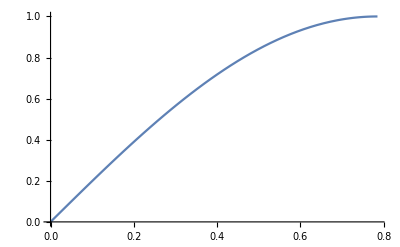

```mathematica
simplePlot
```

```mathematica
simplePlotFullForm = FullForm[simplePlot];
```

```mathematica
Length[List@@simplePlot]
```

2

```mathematica
simplePlotInputForm = InputForm[simplePlot];
```

```mathematica
Length[List@@simplePlotInputForm]
```

1

```mathematica
??FullForm
```

```mathematica
??InputForm
```

```mathematica
Red//FullForm
Red//InputForm
```

RGBColor[1,0,0]

RGBColor[1, 0, 0]

```mathematica
ToExpression@"List[Green, Blue]"
```

{RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
ToString[InputForm@simplePlot]
```

### A parenthesis - PrintDefinitions

PrintDefinitions, a function from the Wolfram Function repository, creates a notebook object for a WL symbol, containing the symbol documentation/definition content.

```mathematica
ResourceFunction["PrintDefinitions"]
```

```mathematica
PrintDefinitions@Graphics
```

yghv2_shm184FrontEndObject[LinkObject["yghv2_shm", 3, 1]]184System`Graphics

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...